```mathematica
CExpressionToNumber[string_]:=ToExpression[StringReplace[string,{"e+":>"*^","e-":>"*^-"}]]
```

## Diversidad

```mathematica
<<MaTeX`
```

```mathematica
Languages={"EN","FR","GE","IT","SP"};LanguageNames={"English","French","German","Italian","Spanish"};
```

```mathematica
Colors=RGBColor@@@({{0,133,171},{255,117,0},{135,0,179},{48,130,5},{163,0,0}}/256);
```

```mathematica
GetData[{l1_,l2_}]:=ReadList["Datos_art/DiversityK/Conjuntos/diversidad_"<>l1<>"-"<>l2<>".txt",Number];GetData[{l1_Integer,l2_Integer},Languages_]:=GetData[{Languages[[l1]],Languages[[l2]]}]
```

```mathematica
data=GetData[pair,Languages];
```

```mathematica
(*Longitudes de los datos*)
Table[Length[GetData[{l1,l2},Languages]],{l1,5},{l2,Delete[Range[5],l1]}]
```

{{265,96,52,54},{269,67,96,57},{52,33,28,11},{65,84,32,189},{104,75,21,289}}

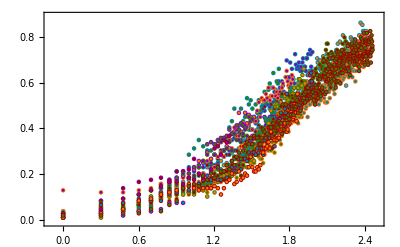

```mathematica
RatioPlot=GoldenRatio;
α=0.01;
Ranges={{-0.1,2.5},{-.01,.89}};
αRanges=(Ranges[[1,2]]-Ranges[[1,1]])/(Ranges[[2,2]]-Ranges[[2,1]]);
{r1=α {αRanges/RatioPlot,1},r2=.6α{αRanges/RatioPlot,1}};
gData=Show[Table[
data=GetData[{l1,l2},Languages];
d2={Log10[#[[1]]],#[[2]]}&/@Transpose[{Range[Length[data]],data}];
Graphics[{Colors[[l1]],Disk[#,r1],Colors[[l2]],Disk[#,r2]}&/@d2]

,{l1,5},{l2,Delete[Range[5],l1]}],Frame->True,AspectRatio->1/RatioPlot,PlotRange->Ranges]
```

```mathematica
?*Move*
```

```mathematica
gData[[1,1,1]]
```

{RGBColor[0, Rational[133, 256], Rational[171, 256]],Disk[{0,0.0091743119266055051},{0.0178543,0.01}],RGBColor[Rational[255, 256], Rational[117, 256], 0],Disk[{0,0.0091743119266055051},{0.0107126,0.006}]}

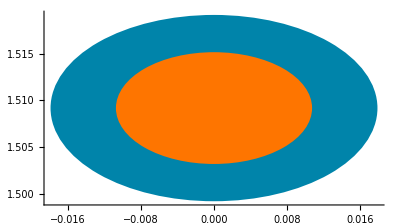

```mathematica
Show[Graphics[Translate[gData[[1,1,1]],{-.0,1.5}]],Axes->True]
```

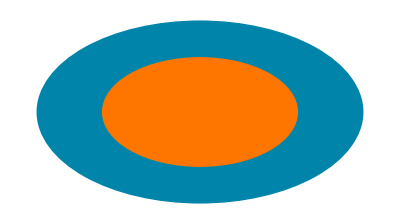

```mathematica
Graphics[gData[[1,1,1]]]
```

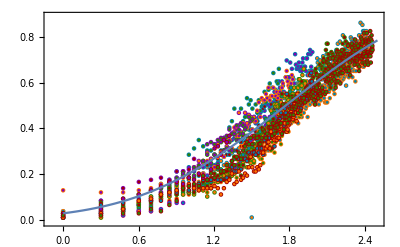

```mathematica
{μ=1.7709,σ=1/0.7661};
Show[{gData,Graphics[Translate[gData[[1,1,1]],{1.5,0}]],Plot[(Erf[(x-μ)/σ]+1)/2,{x,0,2.5}]}]
```

```mathematica
AllData=Table[
data=GetData[{l1,l2},Languages];
{Log10[#[[1]]],#[[2]]}&/@Transpose[{Range[Length[data]],data}]
,{l1,5},{l2,Delete[Range[5],l1]}];
{μAllData,σAllData}=Module[{σf,μf},FindFit[Flatten[AllData,2],(Erf[(x-μf)/σf]+1)/2,{μf,σf},x][[All,2]]]
```

{1.81560945084124724,1.17604338335489627}

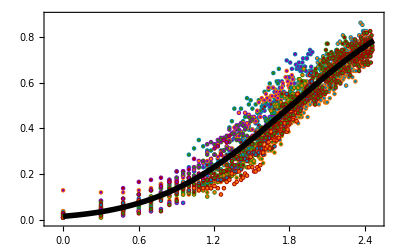

```mathematica
gData2=Show[{gData,Plot[(Erf[(x-μAllData)/σAllData]+1)/2,{x,0,2.47},PlotStyle->{Black,Thickness[0.01]}]}]
```

```mathematica
AllFits=Table[
data=GetData[{l1,l2},Languages];
dAll={Log10[#[[1]]],#[[2]]}&/@Transpose[{Range[Length[data]],data}];
FindFit[dAll,(Erf[(x-μf2)/σf2]+1)/2,{μf2,σf2},x][[All,2]]
,{l1,5},{l2,Delete[Range[5],l1]}];
```

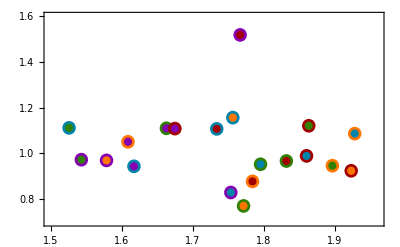

```mathematica
RatioPlot=GoldenRatio;
α=0.03;
Ranges={{1.5,1.96},{.7,1.6}};
αRanges=(Ranges[[1,2]]-Ranges[[1,1]])/(Ranges[[2,2]]-Ranges[[2,1]]);
{r1=α {αRanges/RatioPlot,1},r2=.6α{αRanges/RatioPlot,1}};
AllFits=Table[
data=GetData[{l1,l2},Languages];
dAll={Log10[#[[1]]],#[[2]]}&/@Transpose[{Range[Length[data]],data}];
p1=FindFit[dAll,(Erf[(x-μf2)/σf2]+1)/2,{μf2,σf2},x][[All,2]];
Graphics[{Colors[[l1]],Disk[#,r1],Colors[[l2]],Disk[#,r2]}&[p1]]
,{l1,5},{l2,Delete[Range[5],l1]}];
gAllFits=Show[AllFits,Frame->True,PlotRange->Ranges,AspectRatio->1/RatioPlot]
```

```mathematica
gBlah=Graphics[{
Text[MaTeX["\\mu"],Scaled[{.3,.45}]],
Text[MaTeX["\\log_{10} k"],Scaled[{.5,-.1}]],
Text[MaTeX["\\sigma" ],Scaled[{.03,.72}],{0,0},{0,1}],Text[MaTeX["d(k)" ],Scaled[{-.06,.5}],{0,0},{0,1}]
}];
```

```mathematica
{multiplicadorV=0.06,xLegend=2.,yLegend=0.4};
glegend=Graphics[
{Table[
{Text[Style["■ ",FontWeight->"Bold",FontSize->20,FontColor->Colors[[l1]]],{xLegend,yLegend-multiplicadorV l1},{1,0}],
Text[LanguageNames[[l1]],{xLegend,yLegend-multiplicadorV l1},{-1,0}]
},{l1,5}]}
];
```

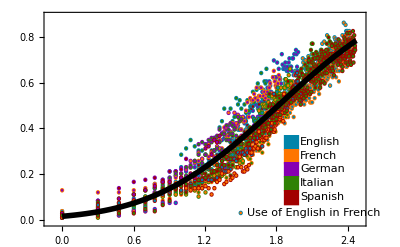

```mathematica
{xEx=1.5,yEx=0.02};
gExample=Graphics[{Translate[gData[[1,1,1]],{xEx,yEx}],Text["Use of English in French",{xEx+.05,yEx+.01},{-1,0}]}];
gDiverse=Show[{gData2,gBlah,glegend,gExample},PlotRangeClipping->False,ImagePadding->{{29,10},{29,1}},Epilog->Inset[gAllFits,{.69,.65},Scaled[{.5,.5}],1.2]]
```

```mathematica
Export["images/Diversity.pdf",gDiverse];
```

## Evolucion de uso

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
<<MaTeX`
```

```mathematica
Languages={"EN","FR","GE","IT","SP"};ls={Language1="EN",Language2="FR"};
Colors=RGBColor@@@({{0,133,171},{255,117,0},{135,0,179},{48,130,5},{163,0,0}}/256);
```

```mathematica
GetData[{l1_,l2_}]:=CExpressionToNumber/@ReadList["Datos_art/Uso/Conjuntos/USO_a"<>l1<>"-"<>l2<>".txt",String];
GetData[{l1_Integer,l2_Integer},Languages_]:=GetData[{Languages[[l1]],Languages[[l2]]}]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{txfonts}"}];
```

```mathematica
ticksX=Table[{i,ToString[1900+i]},{i,0,100,20}];
ticksY=Table[i,{i,0,10,1}];
```

```mathematica
LanguageNames={"English","French","German","Italian","Spanish"};
```

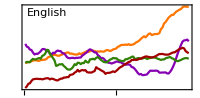
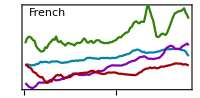
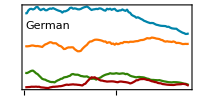
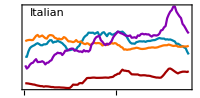
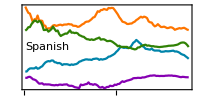

```mathematica
CoordenadasTexto={{.15,.9},{.15,.9},{.15,.75},{.15,.9},{.15,.5}};
l1=1;
g1=Table[
Show[{Graphics[{Text[LanguageNames[[l1]],Scaled[CoordenadasTexto[[l1]]]],
Text[MaTeX["\\text{Year}"],Scaled[{.5,-.25}]],
Text[MaTeX["U_{\\times 10^{-3}}" ],Scaled[{-.08,.5}],{0,0},{0,1}]
}],Table[
pair={l1,l2};
data=10GetData[pair,Languages];
ListPlot[data,Joined->True,PlotStyle->Colors[[pair[[2]]]],PlotRange->All],{l2,Delete[Range[5],l1]}]},PlotRange->All,PlotRangeClipping->False,Frame->True,FrameTicks->{ticksX,ticksY,None,None},Axes->False,AspectRatio->.8/GoldenRatio,ImageSize->200],{l1,5}]
Table[Export["images/prevolucion"<>ToString[l1]<>".pdf",g1[[l1]]],{l1,5}];
```

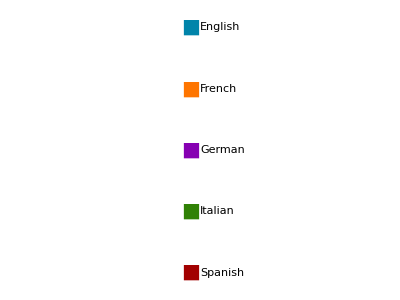

```mathematica
{multiplicadorV=0.1};
glegend=Show[Graphics[
Table[
{Text[Style["■ ",FontWeight->"Bold",FontSize->20,FontColor->Colors[[l1]]],{0,-multiplicadorV l1},{1,0}],
Text[LanguageNames[[l1]],{0,-multiplicadorV l1},{-1,0}]
},{l1,5}]
]]
```

```mathematica
Export["images/prevolucion_legendas.pdf",glegend];
```

## Pre figura de las columnas con el numero de palabras uqe migran

```mathematica
{n=5,y=11};
d=Table[
{d1=Table[RandomInteger[20],{y},{n-1}],
d2=Table[RandomInteger[80],{y}]},{n}];
```

```mathematica
claves={"EN","FR","GE","IT","SP"}
```

{EN,FR,GE,IT,SP}

```mathematica
d[[1]]
```

{{{7,5,6,8},{1,3,4,13},{13,5,8,5},{18,18,16,16},{10,2,9,9},{6,2,11,12},{12,20,5,19},{20,16,12,11},{20,14,0,19},{0,13,6,5},{16,11,20,20}},{59,11,57,51,59,63,51,22,4,75,47}}

```mathematica
ds={ReadList["!cut  DATOS/NW1_"<>#<>" -c 3-",Number,RecordLists->True],ReadList["!cut  DATOS/NW2_"<>#<>" -c 3-",Number,RecordLists->True]}&/@claves;
```

```mathematica
ticksx=Table[{i,10(i-1)+1900},{i,1,y,2}];
```

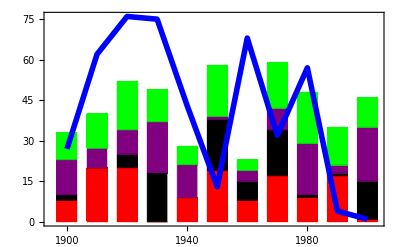

```mathematica
gDibujos[d_,l_,Colors_]:=Module[{gbc,gl},
gbc=BarChart[d[[l,1]],ChartLayout->"Stacked",ChartStyle->Delete[Colors,l],BarSpacing->.5,Axes->None];gl=ListPlot[d[[l,2]],Joined->True,PlotStyle->{Colors[[l]],Thickness[0.01]}];Show[{gbc,gl},Frame->True,FrameTicks->{ticksx,Automatic,None,None},PlotRange->All,PlotRangePadding->None]
]
Colors={Red,Blue,Black,Purple,Green};
gDibujos[d,l,Colors]
```

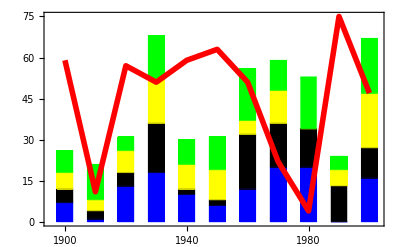
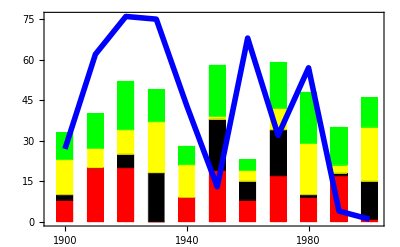
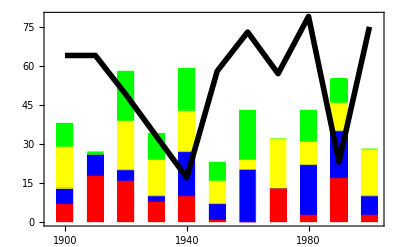
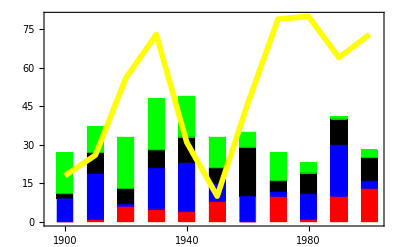
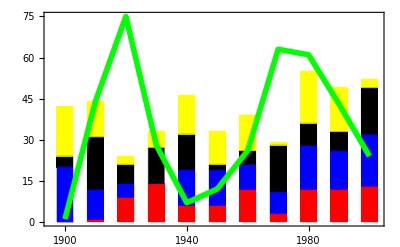

```mathematica
Table[gDibujos[d,l,Colors],{l,5}]
```